## MKP v 2D, priehyb membrany

Fyzikalne parametre

```mathematica
a[{x_,y_}]=1;(*tuhost membrany [N/m], Yungov modul*)
f[{x_,y_}]=0;(*intenzita vonkajsich sil [N/m^2], plošné zaťaženie*)
```

```mathematica
L2chyby={};
Clear[L2chyby,ENchyby,nxList,nyList,nList,nEList];

L2chyby={};
ENchyby={};

nxList={};
nyList={};
nList={};
nEList={};
```

Geometricke parametre

```mathematica
Clear[x,y];
sirka=2;vyska=3/2;(*rozmery obdlznika*)
x1=0;x2=x1+sirka;
y1=0;y2=y1+vyska;
ΩΩ=Polygon[{{x1,y1},{x2,y1},{x2,y2},{x1,y2}}];(*vypoctova oblast*)
Γ1=Line[{{x1,y1},{x2,y1}}];(*1. cast hranice*)
Γ2=Line[{{x2,y1},{x2,y2}}];(*2. cast hranice*)
Γ3=Line[{{x2,y2},{x1,y2}}];(*3. cast hranice*)
Γ4=Line[{{x1,y2},{x1,y1}}];(*4. cast hranice*)
Γ=RegionUnion[Γ1,Γ2 ,Γ3,Γ4];(*hranica*);
```

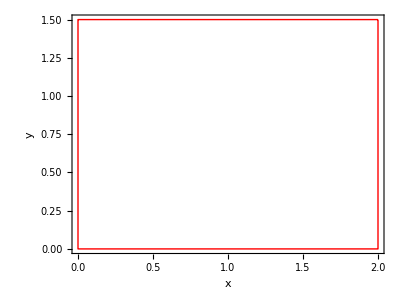

```mathematica
Γplot=RegionPlot[Γ,BoundaryStyle->{Thick,Red},AspectRatio->Automatic,FrameLabel->{Style[x,Large],Style[y,Large]}]
```

Parametre okrajovych podmienok (Dirichlet)

```mathematica
Clear[g1,g2,g3,g4];
```

```mathematica
Clear[g3,x,y];

g1[{x_,y_}]=0(*Sin[Pi (x-x1)/(x2-x1)]*); (*okrajova podmienka na Γ1*)
g2[{x_,y_}]=0 (*0.5Sin[3Pi (y-y1)/(y2-y1)]*); (*okrajova podmienka na Γ2*)
g3[{x_,y_}]=Sin[Pi (x-x1)/(x2-x1)];(*x(2-x)*); (*okrajova podmienka na Γ3*)
g4[{x_,y_}]=0(*Sin[2*Pi (y-y1)/(y2-y1)*); (*okrajova podmienka na Γ4*);
```

```mathematica
(*vykreslenie okrajovych podmienok, tam kde g* nie je nula*)
g1plot=ParametricPlot3D[{x,y1,g1[{x,y1}]},{x,x1,x2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
g2plot=ParametricPlot3D[{x2,y,g2[{x2,y}]},{y,y1,y2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
g3plot=ParametricPlot3D[{x,y2,g3[{x,y2}]},{x,x1,x2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
g4plot=ParametricPlot3D[{x1,y,g4[{x1,y}]},{y,y1,y2},PlotStyle->{Thick,Red},AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
```

```mathematica
gplot=Show[g1plot,g2plot,g3plot,g4plot,PlotRange->All]
```

-Graphics3D-

Presne riesenie (platne pre g-cka rovne sinusom - s akymkolvek poctom “kopcekov” a a=1, f=0)

```mathematica
uA[{x_,y_}]=
g1[{x,y1}]Sinh[Pi/(x2-x1)(y2-y)]/Sinh[Pi(y2-y1)/(x2-x1)]+
g2[{x2,y}]Sinh[3Pi/(y2-y1)(x-x1)]/Sinh[3Pi(x2-x1)/(y2-y1)]+
g3[{x,y2}]Sinh[Pi/(x2-x1)(y-y1)]/Sinh[Pi(y2-y1)/(x2-x1)]+
g4[{x1,y}]Sinh[Pi/(y2-y1)(x2-x)]/Sinh[Pi(x2-x1)/(y2-y1)]
```

Csch[(3 π)/4] Sin[(π x)/2] Sinh[(π y)/2]

```mathematica
uAplot3D=Plot3D[uA[{x,y}],{x,y}∈ΩΩ,AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]},BoxRatios->Automatic,PlotStyle->{Red,Opacity[0.5]},PlotRange->All]
```

-Graphics3D-

MKP, diskretizacia oblasti

```mathematica
nx=6;(*pocet dielokov v smere x*)
ny=4;(*pocet dielokov v smere y*)
hx=sirka/nx;(*dlzka dielokov v smere x*)
hy=vyska/ny;(*dlzka dielokov v smere y*)


(*globalne uzlove body*)
(*Zoznam uzlov R:najprv po x,potom po y, po riadkoch*)
 (*RI=(XI,YI), dvojice súradníc*)
R=Flatten[
Table[
{x1+i*hx,y1+j*hy},
{j,0,ny},
{i,0,nx}],1
];
n=Length[R];(*pocet neznamych globalnych uzlovych hodnot, (nx+1)*(ny+1)*)
R
```

{{0,0},{1/3,0},{2/3,0},{1,0},{4/3,0},{5/3,0},{2,0},{0,3/8},{1/3,3/8},{2/3,3/8},{1,3/8},{4/3,3/8},{5/3,3/8},{2,3/8},{0,3/4},{1/3,3/4},{2/3,3/4},{1,3/4},{4/3,3/4},{5/3,3/4},{2,3/4},{0,9/8},{1/3,9/8},{2/3,9/8},{1,9/8},{4/3,9/8},{5/3,9/8},{2,9/8},{0,3/2},{1/3,3/2},{2/3,3/2},{1,3/2},{4/3,3/2},{5/3,3/2},{2,3/2}}

```mathematica
nE=2*nx*ny;(*počet elementov, každý obdlždnik rozdelí na trojuholník, preto 2krát*)
(*konektivita:B[[e]]={n1,n2,n3} globálne uzly trojuholníka*)
B=Table[{0,0,0},nE];(*B(e,i) = globalne cislo i-teho bodu na e-tom elemente *)

(*
- riadok má nx + 1 elementov
- Spodný riadok elementu je j-1,vrchný je j *)
(*každý element e obsahuje tri globálne uzly {n1,n2,n3}*)
e = 1;
For[j=1,j<=ny,j++,
For[i=1,i<=nx,i++,
n1=(j-1)*(nx+1)+i;  (*ľavý spodný uzol*)
n2=n1+1; (*pravý spodný uzol, vpravo vedľa n1*)
n3=n1+(nx+1); (*ľavý horný uzol, nad n1*)
n4=n3+1; (*pravý horný uzol, nad n2*)

(*rozdelím štvoruholník, na ňom 2 elementy (trojuholníky)*)
B[[e]]={n1,n2,n4};(*prvý trojuholník - nepárny 1,3,5*)
e++;
B[[e]]={n1,n4,n3};(*druhý trojuholník - párny 2,4,6*)
e++;
];
];
B //MatrixForm;
n=Length[R];
nE=Length[B];

Print["n  = ",n];
Print["nE = ",nE];
```

n  = 35

nE = 48

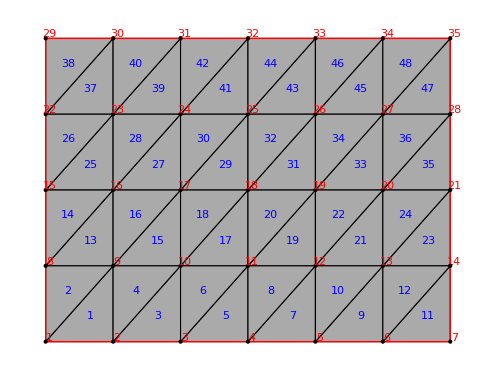

```mathematica
(*elementy ako geometrické regióny*)
Ω=Table[Triangle[R⟦B⟦e⟧⟧],{e,1,nE}];(*elementy*)
Rplot=Graphics[Point[R]];(*vykreslenie uzlovych bodov*)
RIDplot=Graphics[{Red,Table[Text[i,R⟦i⟧+{0.02,0.02}],{i,1,n}]}];(*vykreslenie cisel uzlovych bodov*)
EdgePlot=Graphics[{FaceForm[None],EdgeForm[Black],Ω}];(*vykreslenie hran*)
ElemPlot=Graphics[{FaceForm[Lighter[Gray]],EdgeForm[Black],Ω}];(*vykreslenie elementov*)
ElemPlotIDplot=Graphics[{Blue,Table[Text[e,Mean[R⟦B⟦e⟧⟧]],{e,1,nE}]}];(*vykreslenie cisel elementov*)
Show[ElemPlot,Γplot,ElemPlotIDplot,Rplot,RIDplot,ImageSize->500]
```

MKP, diskretizacia okrajovej podmienky

```mathematica
dirichlet=Table[False,{i,1,n}]; (*najprv všetky žiaden dirichlet, každý globálny uzol*)

(*dirichlet(i)=True,ak je R(i) na hranici oblasti*)

(*Najprv si vyberiem do poľa uzly,ktoré sú na hranici a potom im pridám danú Dirichletovu hodnotu*)
For[
i=1,i<=n,i++,
(*i-ty uzol, [i,1]->x,  [i,2]->y*)
x=R[[i,1]]; (*R dvojprvkový zoznam*)
y=R[[i,2]];
If[
x==x1||x==x2||y==y1||y==y2,
dirichlet[[i]]=True;
];
];
dirichlet;

(*Dirichlet hodnoty*)
g=Table[0.,{n}];

For[
i=1,i<=n,i++,
x=R[[i,1]]; (*x suradnica*)
y=R[[i,2]]; (*y suradnica*)
If[
y==y1,g[[i]]=g1[{x,y}]
];(*dolná hrana*)
If[
x==x2,g[[i]]=g2[{x,y}]
];(*pravá hrana*)
If[
y==y2,g[[i]]=g3[{x,y}]
];(*horná hrana*)
If[
x==x1,g[[i]]=g4[{x,y}]
];(*ľavá hrana*)
];

(*kolkaty uzol, jeho suradnice, jeho hodnoty na hranici*)
Table[{i,R[[i]],g[[i]]},{i,1,n}]
```

{{1,{0,0},0},{2,{1/3,0},0},{3,{2/3,0},0},{4,{1,0},0},{5,{4/3,0},0},{6,{5/3,0},0},{7,{2,0},0},{8,{0,3/8},0},{9,{1/3,3/8},0.},{10,{2/3,3/8},0.},{11,{1,3/8},0.},{12,{4/3,3/8},0.},{13,{5/3,3/8},0.},{14,{2,3/8},0},{15,{0,3/4},0},{16,{1/3,3/4},0.},{17,{2/3,3/4},0.},{18,{1,3/4},0.},{19,{4/3,3/4},0.},{20,{5/3,3/4},0.},{21,{2,3/4},0},{22,{0,9/8},0},{23,{1/3,9/8},0.},{24,{2/3,9/8},0.},{25,{1,9/8},0.},{26,{4/3,9/8},0.},{27,{5/3,9/8},0.},{28,{2,9/8},0},{29,{0,3/2},0},{30,{1/3,3/2},1/2},{31,{2/3,3/2},(√3)/2},{32,{1,3/2},1},{33,{4/3,3/2},(√3)/2},{34,{5/3,3/2},1/2},{35,{2,3/2},0}}

MKP, zostrojenie linearnych aproximacnych funkcii

MKP, zostrojenie lokalnych matic a pravych st ran

```mathematica
(*lokálne matice*)
LokK=ConstantArray[0.,{nE,3,3}];
LokF=ConstantArray[0.,{nE,3}];
Clear[x,y];

Psi=ConstantArray[0.,{nE,3,3}]; (*pre každý element 3 funkie*)
```

```mathematica
(*každý element 3 aproximačné funkcie*)
AbsoluteTiming[
Do[
(*uzly elementu e, ktoré tvoria trojuholník*)
n1=B[[e,1]];
n2=B[[e,2]];
n3=B[[e,3]];

(*súradnice uzlov*)
x1e=R[[n1,1]];y1e=R[[n1,2]];
x2e=R[[n2,1]];y2e=R[[n2,2]];
x3e=R[[n3,1]];y3e=R[[n3,2]];

(*alphaE,betaE,gammaE,DE*)
a1=x2e*y3e-x3e*y2e;
a2=x3e*y1e-x1e*y3e;
a3=x1e*y2e-x2e*y1e;
alpha={a1,a2,a3};

b1=y2e-y3e;
b2=y3e-y1e;
b3=y1e-y2e;
beta={b1,b2,b3};

(*pre istotu premenované,aby sa nebilo s g1 z hranice*)
g1e=-(x2e-x3e);
g2e=-(x3e-x1e);
g3e=-(x1e-x2e);
gamma={g1e,g2e,g3e};

De=a1+a2+a3;(*2*plocha trojuholníka*)

(*ako výrazy*)
Psi[[e,1]]=(a1+b1*x+g1e*y)/De;
Psi[[e,2]]=(a2+b2*x+g2e*y)/De;
Psi[[e,3]]=(a3+b3*x+g3e*y)/De;

   ,{e,1,nE}
]
];
```

Overenie kronecker delty

```mathematica
Print["--- Kronecker delta kontrola: Psi_i(vrchol_j) ---"];

Do[
Module[
{n1,n2,n3,uzly,hodnoty},
n1=B[[e,1]];
n2=B[[e,2]];
n3=B[[e,3]];
uzly={n1,n2,n3};

hodnoty=Table[
N@(Psi[[e,i]]/. {x->R[[uzly[[j]],1]],y->R[[uzly[[j]],2]]}),
{i,1,3},{j,1,3}
];
Print["e=",e," uzly=",uzly,"  Psi_i(vrchol_j)="];
Print[MatrixForm[hodnoty]];],{e,1,Min[3,nE]}   (* prvé 3 elementy*)
];
```

--- Kronecker delta kontrola: Psi_i(vrchol_j) ---

e=1 uzly={1,2,9}  Psi_i(vrchol_j)=

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

e=2 uzly={1,9,8}  Psi_i(vrchol_j)=

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

e=3 uzly={2,3,10}  Psi_i(vrchol_j)=

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

Zostrejenie matice tuhosti a PS na elemente

```mathematica
Clear[x,y];
Do[
LokK[[e]]=Table[
Integrate[a[{x,y}]*(D[Psi[[e,i]],x]*D[Psi[[e,j]],x]+D[Psi[[e,i]],y]*D[Psi[[e,j]],y]),
Element[{x,y},Ω[[e]]]],
{i,1,3},
{j,1,3}],
{e,1,nE}
];

(*Do[
LokF[[e]]=Table[
Integrate[f[{x,y}]*Psi[[e,i]][x,y],
Element[{x,y},Ω[[e]]]],
{i,1,3}],
{e,1,nE}
];*)

Do[
LokF[[e]]=Table[
Integrate[f[{x,y}]*Psi[[e,i]],
Element[{x,y},Ω[[e]]]],
{i,1,3}],
{e,1,nE}
];
LokK[[1]]  //MatrixForm
LokF[[1]]//MatrixForm
```

(9/16 | -9/16 | 0
-9/16 | 145/144 | -4/9
0 | -4/9 | 4/9)

(0
0
0)

```mathematica
LokK⟦1⟧//MatrixForm (*lokálna tuhosť 1.trojuholníka*)
LokF⟦1⟧//MatrixForm(*Ps 1.trojuholníka*)
LokK⟦2⟧//MatrixForm
LokF⟦2⟧//MatrixForm
LokK⟦3⟧//MatrixForm

Psi[[1]] (*aproximačné funkcie 1 elementu*)
```

(9/16 | -9/16 | 0
-9/16 | 145/144 | -4/9
0 | -4/9 | 4/9)

(0
0
0)

(4/9 | 0 | -4/9
0 | 9/16 | -9/16
-4/9 | -9/16 | 145/144)

(0
0
0)

(9/16 | -9/16 | 0
-9/16 | 145/144 | -4/9
0 | -4/9 | 4/9)

{8 (1/8-(3 x)/8),8 ((3 x)/8-y/3),(8 y)/3}

MKP, zostrojenie globalnych matic a pravych stran

```mathematica
GlobK=ConstantArray[0.,{n,n}];
GlobF=ConstantArray[0.,n];
Print["n = ",n];
Print["nE = ",nE];
Print["Max B = ",Max[Flatten[B]]];
Print["Rozmer GlobK = ",Dimensions[GlobK]];
Print["dlzka GlobF = ",Length[GlobF]];



For[
e=1,e<=nE,e++,
(*globálne čísla uzlov elementu e, riadok*)

(*{n1,n2,n3} globálne čísla uzlov*)
n1=B[[e,1]];
n2=B[[e,2]];
n3=B[[e,3]];

(*idem cez lokálne uzly i,j=1..3, stlpec*)
For[
i=1,i<=3,i++,
gi=B[[e,i]];(*lokálny i->globálny gi*)

(*montujem vektor pravých strán, tam kde mi zodpovedá globálny index, Fei ide do GlobF[gi]*)
GlobF[[gi]]+=LokF[[e,i]];

For[
j=1,j<=3,j++,
gj=B[[e,j]];(*lokálny j->globálny gj*)

(*montujem vektor pravých strán, tam kde mi zodpovedá globálny index, Keij ide do GlobF[gi,gj]*)
GlobK[[gi,gj]]+=LokK[[e,i,j]];
];
];
];

(*index Glob uzla, Je tam dirichlet?, PS v uzly i*)
Table[{i,dirichlet[[i]],GlobF[[i]],Norm[GlobK[[i]]]},{i,1,n}]
```

n = 35

nE = 48

Max B = 35

Rozmer GlobK = {35,35}

dlzka GlobF = 35

{{1,True,0.,1.23607},{2,True,0.,2.34066},{3,True,0.,2.34066},{4,True,0.,2.34066},{5,True,0.,2.34066},{6,True,0.,2.34066},{7,True,0.,1.23607},{8,True,0.,2.39091},{9,False,0.,4.50938},{10,False,0.,4.50938},{11,False,0.,4.50938},{12,False,0.,4.50938},{13,False,0.,4.50938},{14,True,0.,2.39091},{15,True,0.,2.39091},{16,False,0.,4.50938},{17,False,0.,4.50938},{18,False,0.,4.50938},{19,False,0.,4.50938},{20,False,0.,4.50938},{21,True,0.,2.39091},{22,True,0.,2.39091},{23,False,0.,4.50938},{24,False,0.,4.50938},{25,False,0.,4.50938},{26,False,0.,4.50938},{27,False,0.,4.50938},{28,True,0.,2.39091},{29,True,0.,1.23607},{30,True,0.,2.34066},{31,True,0.,2.34066},{32,True,0.,2.34066},{33,True,0.,2.34066},{34,True,0.,2.34066},{35,True,0.,1.23607}}

```mathematica
GlobK//MatrixForm;
GlobF//MatrixForm;
```

MKP, zahrnutie okrajovych podmienok

```mathematica
GlobK=Normal[GlobK];  

For[i=1,i<=n,i++,
If[
dirichlet[[i]], (*Dirichlet ui=gi*)
(*vynulujem riadok a stĺpec patriaci uzlu i*)
GlobK[[i,All]]=0; (*vynulujem RIADOK*)
(*GlobK[[All,i]]=0;*)
(*diagonálu nastavím na 1*)
GlobK[[i,i]]=1.; (*jednotka na diagonále*)

(*pravá strana=predpísaná hodnota*)
GlobF[[i]]=g[[i]];
];
];




GlobK//MatrixForm;
GlobF//MatrixForm;
```

MKP, riesenie rovnic, konstrukcia priblizneho riesenia, zobrazenie presneho aj priblizneho riesenia

```mathematica
Clear[x,y];
U=LinearSolve[GlobK,GlobF]//N;(*riesenie systemu*)
Table[{i,R[[i]],U[[i]]},{i,1,n}];
```

```mathematica
RU=Table[Append[R⟦i⟧,U⟦i⟧],{i,1,n}];(*konstrukcia 3D bodov pre vykreslenie riesenia ako grafu v 3D*)
```

```mathematica
(* konstrukcia riesenia na elementoch*)
UNlok[e_][x_,y_]:=Module[
{uLoc=U[[B[[e]]]]},(*lokalne uzlove hodnoty na elemente e*)
Sum[uLoc[[i]]*Psi[[e,i]],
{i,1,3}]
];


(* konstrukcia celkoveho MKP riesenia*)
UNglob[{x_,y_}]:=Piecewise[Table[{UNlok[e][x,y],{x,y}∈Ω[[e]]},{e,1,nE}]];
```

```mathematica
AbsoluteTiming[
UNlokPlot[e_]:=Plot3D[UNlok[e][x,y],{x,y}∈Ω⟦e⟧,PlotPoints->2,AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]}];
Uplot3D=Show[gplot,Table[UNlokPlot[e],{e,1,nE}],BoxRatios->Automatic];
Uplot3Dpoints=ListPointPlot3D[Table[RU⟦i⟧,{i,1,n}],AxesLabel->{Style[x,Large],Style[y,Large],Style[u,Large]},PlotStyle->{Blue,PointSize[0.02]}];(*vykreslenie uzlovych hodnot*)
Uplot3Dedges=Graphics3D[{FaceForm[None],EdgeForm[{Thick,Black}],Table[Triangle[RU⟦B⟦e⟧⟧],{e,1,nE}]}];(*vykreslenie hran trojuholnikov*)


{uMin,uMax}=MinMax[U];
UNlokContourPlot[e_]:=ContourPlot[UNlok[e][x,y],{x,y}∈Ω⟦e⟧,FrameLabel->{Style[x,Large],Style[y,Large]},Contours->Table[uMin+i(uMax-uMin)/20,{i,0,20}],AspectRatio->Automatic,ColorFunction->(ColorData["TemperatureMap",(#-uMin)/(uMax-uMin)]&),ColorFunctionScaling->False];
UcontourPlot=Show[Table[UNlokContourPlot[e],{e,1,nE}]];
]
```

{24.9031,Null}

```mathematica
Show[Uplot3D,uAplot3D,Uplot3Dedges,Uplot3Dpoints,gplot,BoxRatios->Automatic,ImageSize->500]
Show[Γplot,UcontourPlot,EdgePlot,ImageSize->500]
```

-Graphics3D-

-Graphics-

```mathematica
(*presné riešenie*)
uAxy[x_,y_]:=uA[{x,y}];

(*L2 norma chyby*)
L2=Sqrt@Sum[NIntegrate[
(UNlok[e][x,y]-uAxy[x,y])^2,Element[{x,y},Ω[[e]]]],{e,1,nE}]

(*gradient presného riešenia*)
graduA[x_,y_]:=Grad[uAxy[xx,yy],{xx,yy}]/. {xx->x,yy->y}


Clear[gradUNlok];
Clear[e]



(*gradient MKP riešenia na elemente e*)
gradUNlok[e_,x_,y_]:=Grad[UNlok[e][x,y],{x,y}];


energetickaChyba=Sqrt@Sum[
NIntegrate[a[{x,y}]*(Norm[(gradUNlok[e,x,y]-graduA[x,y])])^2,
Element[{x,y},Ω[[e]]]
],{e,1,nE}
]
```

0.0225031

0.351486

```mathematica
AppendTo[L2chyby,L2];
AppendTo[ENchyby,energetickaChyba];
AppendTo[nxList,nx];
AppendTo[nyList,ny];
AppendTo[nList,n];
AppendTo[nEList,nE];
```

```mathematica
L2EOC=Table[Log2[L2chyby[[i]]/L2chyby[[i+1]]],{i,Length[L2chyby]-1}]
ENEOC=Table[Log2[ENchyby[[i]]/ENchyby[[i+1]]],{i,Length[ENchyby]-1}]
```

{1.87888}

{0.934601}

```mathematica
L2chyby
ENchyby
nxList
nyList
nList (*pocet neznamych globalnych uzlovych hodnot velkosť R*)
nEList (*počet elementov*)
L2EOC
ENEOC
```

{0.082764,0.0225031}

{0.671817,0.351486}

{3,6}

{2,4}

{12,35}

{12,48}

{1.87888}

{0.934601}

```mathematica
labels={{"nx","ny","n","nE","L2 chyba","EOC L2","Energ. chyba","EOC Energ."}};
table=Table[{3 2^(i-1),2 2^(i-1),(3 2^(i-1)+1)(2 2^(i-1)+1),12 2^(2(i-1)),AccountingForm[L2chyby⟦i⟧,4],If[i==1,"",AccountingForm[L2EOC⟦i-1⟧,4]],AccountingForm[ENchyby⟦i⟧,4],If[i==1,"",AccountingForm[ENEOC⟦i-1⟧,4]]},{i,1,Length[L2chyby]}];
plotTable=Grid[Join[labels,table],Frame->All,Alignment->{{Right,Left,Left,Left,Left}},Background->{{Yellow,Yellow,Yellow,Yellow,None},{Yellow,None}}]
```

nx | ny | n | nE | L2 chyba | EOC L2 | Energ. chyba | EOC Energ.
3 | 2 | 12 | 12 | 0.08276 |  | 0.6718 | 
6 | 4 | 35 | 48 | 0.0225 | 1.879 | 0.3515 | 0.9346